```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/量子化学实验报告/figures"];
```

```mathematica
list1={{418.131,"HF 6-31G"},{420.686,"B3LYP 6-31G（DFT）"},{9.48884*10^-2,"PM6 (Semi-empirical)"}}
```

{{418.131,HF 6-31G},{420.686,B3LYP 6-31G（DFT）},{0.0948884,PM6 (Semi-empirical)}}

```mathematica
"Methods.eps"~Export~BarChart[#1,ChartLabels->Placed[#2,Top],ImageSize->Large,Axes->False,Frame->True,AxesLabel->{"Type","Energy/Hartree"}]&@@Transpose[list1]
```

Methods.eps

```mathematica
list2=Transpose@{{{418.131,420.686},"6-31G"},{{415.961,418.501},"3-21G"},{{418.340,420.855},"cc-pVDZ"},{{418.186,420.763},"LanL2DZ"}}
```

{{{418.131,420.686},{415.961,418.501},{418.34,420.855},{418.186,420.763}},{6-31G,3-21G,cc-pVDZ,LanL2DZ}}

```mathematica
"Sets.eps"~Export~BarChart[#1,ChartLabels->Placed[#2,Top],ChartLegends->{"HF","DFT"},ImageSize->Large,Axes->False,Frame->True,FrameLabel->{"Type","Energy/Hartree"},PlotRange->{Automatic,{0,420}}]&@@list2
```

Sets.eps

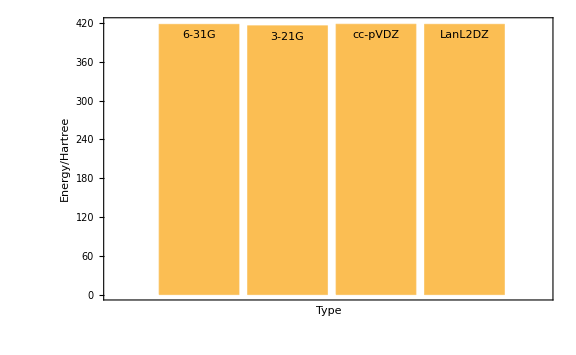

```mathematica
BarChart[#1,ChartLabels->Placed[#2,Top],ImageSize->Large,Axes->False,Frame->True,FrameLabel->{Style["Type",20],Style["Energy/Hartree",20]},PlotRange->{Automatic,{0,420}}]&@@list2
```

```mathematica
"benzoicmethanolIR.eps"~Export~ListLinePlot[{{#1,#2}&@@@Cases[Import["/Volumes/WALTER FENG/Gaussian/benzoicmethanolhf_ir.txt","Table"],{_Real,_Real,_Real}],{#1,#2}&@@@Cases[Import["/Volumes/WALTER FENG/Gaussian/2nd-pack/benzoicmethanoldft_ir.txt","Table"],{_Real,_Real,_Real}]},PlotRange->All,Frame->True,PlotStyle->{{Black,Thickness[0.002],Dashed},{Black,Thickness[0.002]}},PlotLegends->{"HF","DFT"},ImageSize->Large]
```

benzoicmethanolIR.eps

```mathematica
"benzoicformateIR.eps"~Export~ListLinePlot[{#1,#2}&@@@Cases[Import["/Volumes/WALTER FENG/Gaussian/benzoic_formate_ir.txt","Table"],{_Real,_Real,_Real}],PlotRange->All,Frame->True,PlotStyle->{Black,Thickness[0.003]},ImageSize->Large,Axes->False]
```

benzoicformateIR.eps

```mathematica
figure=-Graphics-
```

-Graphics-

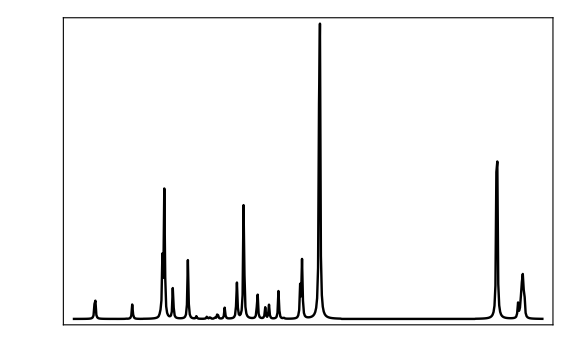

```mathematica
graph=ListLinePlot[{#1,#2}&@@@Cases[Import["/Volumes/WALTER FENG/Gaussian/benzoic_formate_ir.txt","Table"],{_Real,_Real,_Real}],PlotRange->All,Frame->True,PlotStyle->{Black,Thickness[0.003]},ImageSize->Large,Axes->False,FrameTicks->False]~Rotate~Pi
```

```mathematica
"benzoicformateIR.eps"~Export~(graph=ListLinePlot[{{#1,#2}&@@@Cases[Import["/Volumes/WALTER FENG/Gaussian/benzoic_formate_ir.txt","Table"],{_Real,_Real,_Real}],{#1,#2}&@@@Cases[Import["/Volumes/WALTER FENG/Gaussian/2nd-pack/benzoic_formatedft_ir.txt","Table"],{_Real,_Real,_Real}]},PlotRange->All,Frame->True,PlotStyle->{{Black,Thickness[0.002],Dashed},{Black,Thickness[0.002]}},PlotLegends->{"HF","DFT"},ImageSize->Large,Axes->False])
```

benzoicformateIR.eps

```mathematica
TableForm[{#2,#1}&@@Transpose[list1]]//TeXForm
```

\begin{array}{ccc}
 \text{HF 6-31G} & \text{B3LYP 6-31G$\unicode{ff08}$DFT$\unicode{ff09}$} & \text{PM6
   (Semi-empirical)} \\
 418.131 & 420.686 & 0.0948884 \\
\end{array}

```mathematica
TableForm[{#2,#1}&@@list2]//TeXForm
```

\begin{array}{cccc}
 \text{6-31G} & \text{3-21G} & \text{cc-pVDZ} & \text{LanL2DZ} \\
 418.131 & 415.961 & 418.34 & 418.186 \\
\end{array}

```mathematica
RunProcess[{"ssh","user@server"},ProcessEnvironment-><|"PATH"->"/usr/local/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/X11/bin:/Library/TeX/texbin"|>]
```

<|ExitCode→255,StandardOutput→,StandardError→Pseudo-terminal will not be allocated because stdin is not a terminal.\r
ssh: Could not resolve hostname server: nodename nor servname provided, or not known\r
|>